# Plotting ‘Population Structure Trees’ onto geographic maps

INSTRUCTIONS

This tools is intended to plot outputs of NetStruct Tree onto geographic maps.

Follow the following steps:
1. In “DataFolder= “ (purple cell below this orange cell), input the folder that contains the output files of NetStruct_Tree 
2. In “CoordinatesFileFolder=”, input the folder that contains the coordinates file
3. In “CoordinatesFileName=”, input the name of the coordinates file (must be a CSV file)
4. Click anywhere in the purple cell and hit Shift+Enter to run the cell. 
5. In the blue cell, set the coordinate range of the requested map under “range=”
6. Set the root node below which clusters will be colored under “rootnode=”. By default, this is set to “1” so that all clusters will be colored. See paper for details.
7. Click anywhere in the blue cell and hit Shift+Enter to generate the map and Population Structure Tree plots.
8. Steps 5-7 can be repeated to fine-tune and generate several maps. There is no need to re-run the purple cell.

OUTPUTS
There are three outputs:
1. A map with the requested coordinate range. Individual samples are colored according to the cluster assignment, shown in the next two outputs
2. The Population Structure tree, with colored assigned to each cluster (see paper)
3. The same Population Structure tree with the number ID of each cluster. These number IDs can be used to select a different root node.

NOTE
The CSV coordinate file should be structured in the following way:
    Each row contains data on a single individual.
    Column 1 - Associated region of the individual (string). This column does not affect map plotting, and could be identical to all individuals.
    Column 2 - ID of individual (string). Should be the same as was used to generate the NetStruct_Tree outputs.
    Column 3 - Latitude (number).
    Column 4 - Longitude (number).

```mathematica
DataFolder="C:\\Users\\gilig\\Documents\\MEGA\\NetStruct_WG_project\\temp\\arabidopsis1\\5\\data";
CoordinatesFileFolder="C:\\Users\\gilig\\Documents\\Mega\\NetStruct_WG_project\\Arabidopsis";
CoordinatesFileName="indlist_new2_with_coords.csv";

SetDirectory[CoordinatesFileFolder];
file1=Import[CoordinatesFileName];
SetDirectory[DataFolder];
file2name=Select[FileNames[],StringTake[#,6]=="1_Comm"&]⟦1⟧;
file2=Import[file2name,"Table"];
tree1=MakeTreeFull[file2,file1];
PrepareData[DataFolder];
```

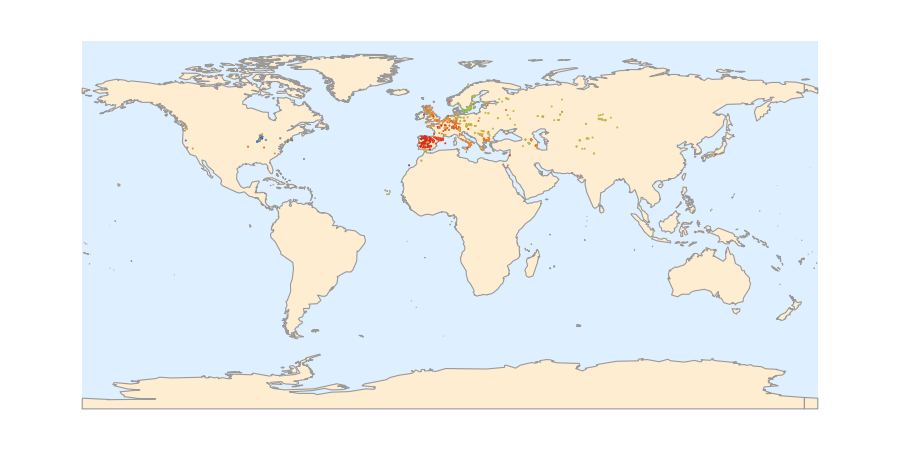

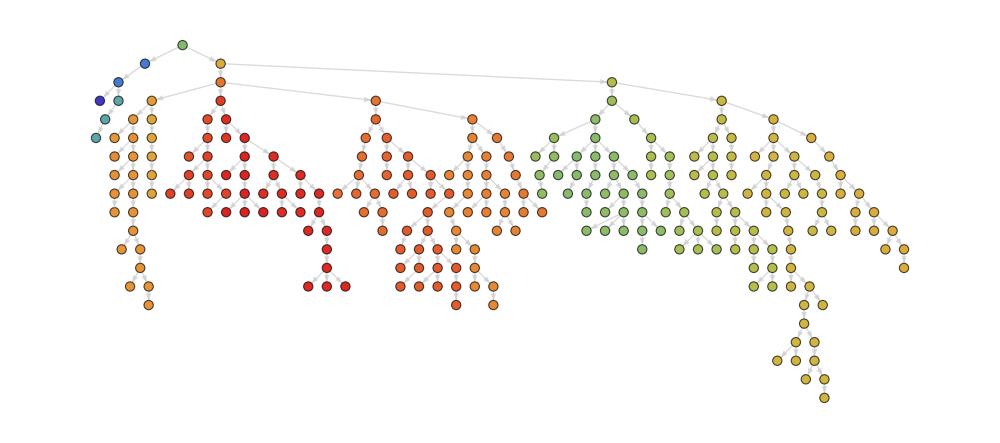

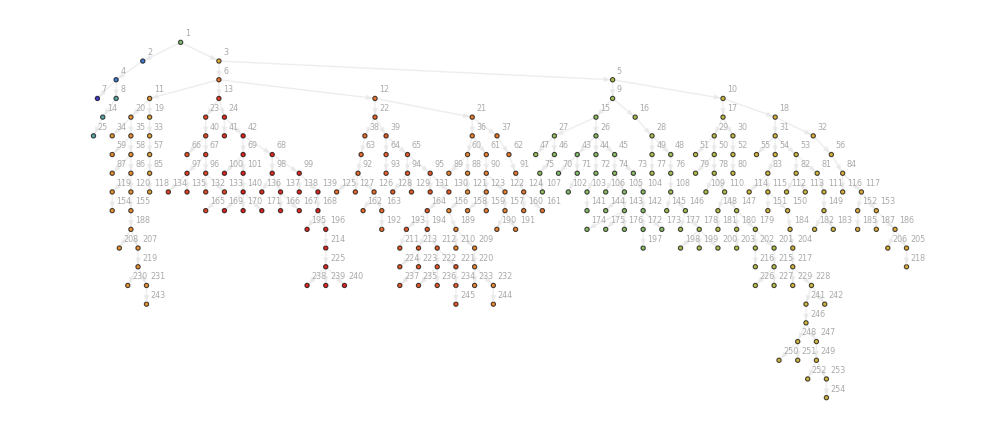

```mathematica
backgroundmap="Coastlines";
range={{-90,90},{-180,180}};(*lat/long - World Map*)
rootnode=1;
pointsize=0.5;
q1=plotmapsAllind[range,rootnode,pointsize,"Rainbow"]
q2=coloredtree2
q3=coloredtree
```

```mathematica
LinetoPie[line_,rescalesize_]:=Module[{},(*Creates piecharts from a line in Amir's format*)
x1=ToExpression[Table[StringDrop[StringReplace[i,"|"->""],StringPosition[StringReplace[i,"|"->""],":"]⟦1,1⟧],{i,line[[2;;Length[lll]+1]]}]];
size=ToExpression[StringTake[line⟦1⟧,{StringPosition[line⟦1⟧,"_"]⟦1,1⟧+1,StringPosition[line⟦1⟧,"_"]⟦2,1⟧-1}]];
labels=Flatten[Take[lll,All,{1}]];
labels=Table[If[x1⟦i⟧/Total[x1]<0.05,"",labels⟦i⟧],{i,Length[labels]}];
pie=PieChart[x1,ChartStyle->colors,ImageSize->300,PlotRangeClipping->False,ImagePadding->{{100,100},{10,10}},PlotRangePadding->30,PlotLabel->Style["n="<>ToString[size],FontSize->15],ChartLabels->Placed[Style[#,10]&/@labels,"VerticalCallout"]];
{pie,x1}
]

MakeTreeFull[file_,file2_]:=Module[{},
lll=Table[StringSplit[StringReplace[a,"|"->""],":"][[1]],{a,Delete[StringSplit[file[[2]],","],1]}];
colors=Table[ColorData["Rainbow"][c],{c,0,1,1/(Length[lll]-1)}];
level=0;
list={};
thislevel={};
sizescale=1.5;
Do[
If[StringTake[f⟦1⟧,10]=="----------",
AppendTo[list,thislevel];thislevel={};level=level+1;,
level=ToExpression[StringTake[f⟦1⟧,{StringPosition[f⟦1⟧,"_"]⟦3,1⟧+1,StringPosition[f⟦1⟧,"_"]⟦4,1⟧-1}]];
entry=ToExpression[StringTake[f⟦1⟧,{StringPosition[f⟦1⟧,"_"]⟦5,1⟧+1,StringPosition[f⟦1⟧,"_"]⟦6,1⟧-1}]];
line=ToExpression[StringTake[f⟦1⟧,{StringPosition[f⟦1⟧,"_"]⟦7,1⟧+1,StringPosition[f⟦1⟧,"_"]⟦8,1⟧-1}]];
parententry=ToExpression[StringTake[f⟦1⟧,{StringPosition[f⟦1⟧,"_"]⟦11,1⟧+1,StringPosition[f⟦1⟧,"_"]⟦12,1⟧-1}]];
parentline=ToExpression[StringTake[f⟦1⟧,{StringPosition[f⟦1⟧,"_"]⟦13,1⟧+1,StringPosition[f⟦1⟧,"_"]⟦14,1⟧-1}]];
parentlevel=ToExpression[StringTake[f⟦1⟧,{StringPosition[f⟦1⟧,"_"]⟦9,1⟧+1,StringPosition[f⟦1⟧,"_"]⟦10,1⟧-1}]];
size=ToExpression[StringTake[f⟦1⟧,{StringPosition[f⟦1⟧,"_"]⟦1,1⟧+1,StringPosition[f⟦1⟧,"_"]⟦2,1⟧-1}]];
threshold=ToExpression[StringTake[f⟦1⟧,{StringPosition[f⟦1⟧,"_"]⟦15,1⟧+1,StringPosition[f⟦1⟧,"_"]⟦16,1⟧-1}]];
linedata=LinetoPie[f,sizescale];
AppendTo[thislevel,{linedata⟦1⟧,{level,entry,line},{parentlevel,parententry,parentline},size,linedata⟦2⟧,threshold}]
]
,{f,file⟦3;;Length[file]⟧}];
AppendTo[list,thislevel];
list=Drop[list,1];
newlist={};
nodeID=2;
Do[
newline={};
Do[(*Add nodeID to each node*)
AppendTo[newline,Join[k,{nodeID}]];
nodeID=nodeID+1
,{k,list⟦l⟧}];
AppendTo[newlist,newline]
,{l,Length[list]}];
newnewlist={};
ll=Flatten[Take[file2,All,{1}]];
pp=Table[Count[ll,i],{i,{labels}}];
Do[(*Find the parent node of each node, and add the parent's node ID to the node data*)
newline={};
If[l==1,newline=Table[Join[k,{1,pp}],{k,newlist⟦l⟧}]];
If[l>1,newline=Table[Join[k,{Select[Flatten[newlist,1],#⟦2⟧==k⟦3⟧&]⟦1,7⟧}],{k,newlist⟦l⟧}]];
AppendTo[newnewlist,newline]
,{l,Length[list]}];
size=Total[pp];
labels=Flatten[Take[lll,All,{1}]];;
pie1=PieChart[pp,ChartStyle->colors,ImageSize->200,PlotRangeClipping->False,ImagePadding->{{100,100},{10,10}},PlotRangePadding->50,PlotLabel->Style["n="<>ToString[size],FontSize->30],ChartLabels->Placed[labels,"RadialCallout"]];(*This is the piechart of the root node*)

g={}; (*Make tree1*)
nodepies={pie1};
Do[
Do[
AppendTo[g,k⟦8⟧->k⟦7⟧];
AppendTo[nodepies,k⟦1⟧]
,{k,l}]
,{l,newnewlist}];
tree1=TreePlot[g,Left,1,VertexRenderingFunction->(Inset[nodepies⟦#2⟧,#1]&),ImageSize->15000,LayerSizeFunction->(5&)];
tree1(*tree1 is the full tree*)
]

PrepareData[folder_]:=(
SetDirectory[folder];
g={}; (*Make tree1*)
l1={};(*level,entry,line corresponding to g *)
nodepies={pie1};
Do[
Do[
AppendTo[g,k⟦8⟧->k⟦7⟧];
AppendTo[l1,k⟦2⟧];
,{k,l}]
,{l,newnewlist}];

l2={};(*Individual numbers in groups corresponding to g*)
Do[
lev=l⟦1⟧;
ent=l⟦2⟧;
line=l⟦3⟧;
fname1="Le_"<>ToString[lev]<>"_En_"<>ToString[ent]<>"_";
fname2=Select[DeleteCases[FileNames[],"AllNodes.txt"],StringTake[#,StringLength[fname1]]==fname1&]⟦1⟧;
ff=Import[fname2,"Table"];
AppendTo[l2,Import[fname2,"Table"]⟦line+1⟧]
,{l,l1}];

gg=Graph[g];
leaves=Flatten[Position[VertexDegree[gg],1]];(*leave numbers*)
leavespos=Table[Position[g,Select[g,#⟦2⟧==l&]⟦1⟧]⟦1,1⟧,{l,leaves}];(*leaf positions in g/l1/l2*)
l3=l2⟦leavespos⟧;
l4=Sort[Flatten[l3]];
)
```

### Create map

```mathematica
leafQ[node_]:=If[MemberQ[leaves,node],True,False]
f[node_,range_]:=((*Assigns ranges for color allocation*)
If[leafQ[node],AppendTo[colores,{node,range}]];
If[!leafQ[node],
daughters=Table[i⟦2⟧,{i,Select[g,#⟦1⟧==node&]}];
Do[
newrange={range⟦1⟧+(range⟦2⟧-range⟦1⟧)/Length[Table[i⟦2⟧,{i,Select[g,#⟦1⟧==node&]}]]*(Position[Table[i⟦2⟧,{i,Select[g,#⟦1⟧==node&]}],d]⟦1,1⟧-1),range⟦1⟧+(range⟦2⟧-range⟦1⟧)/Length[Table[i⟦2⟧,{i,Select[g,#⟦1⟧==node&]}]]*(Position[Table[i⟦2⟧,{i,Select[g,#⟦1⟧==node&]}],d]⟦1,1⟧)};
f[d,newrange];
,{d,daughters}];
];
)

indcolor[i_,colores_]:=(
com=Select[l3,MemberQ[#,i]&]⟦1⟧;(*communnity composition of i*)
compos=Position[l2,com]⟦1,1⟧+1;
rr=Select[colores,#⟦1⟧==compos&];
If[rr=={},color=2,color=rr⟦1,2⟧
];
color
)

ccc[xx_,colorscheme_]:=Which[colorscheme=="VisibleSpectrum",If[xx==2,Lighter[Gray,0.6],ColorData["VisibleSpectrum"][420+(690-420)xx]],colorscheme=="CMYKColors",If[xx==2,Lighter[Gray,0.6],ColorData[colorscheme][0+0.8xx]],True,If[xx==2,Lighter[Gray,0.6],ColorData[colorscheme][xx]]]



coords[i_]:=file1⟦i+1,3;;4⟧

plotmap[range_,rootnode_,pointsize_,colorscheme_]:=Module[{},
colornode=rootnode;
colores={};
f[colornode,{0,1}];
colores=Sort[colores];
colores=Table[{r⟦1⟧,Mean[r⟦2⟧]},{r,colores}];
l6=Table[{i,indcolor[i,colores],coords[i]},{i,l4}];(*An individual list with colors and coordinates*)
l7=Select[l6,(range⟦1,1⟧<#⟦3,1⟧<range⟦1,2⟧)&&(range⟦2,1⟧<#⟦3,2⟧<range⟦2,2⟧)&];(*Select the individuals in the range*)
psize[l_,p_]:=If[l⟦2⟧==2,p/2,p];
colors=Table[r⟦1⟧->ccc[r⟦2⟧,colorscheme],{r,colores}];
colors=Table[If[MemberQ[Flatten[Take[colores,All,{1}]],i],Select[colors,#⟦1⟧==i&]⟦1⟧,i->Directive[Lighter[Gray,0.8],EdgeForm[None]]],{i,VertexCount[g]}];
colors2=Table[If[MemberQ[Flatten[Take[colores,All,{1}]],i],Select[colors,#⟦1⟧==i&]⟦1⟧,i->Directive[Lighter[Gray,0.8],EdgeForm[None]]],{i,VertexCount[g]}];
coloredtree=Graph[g,VertexLabels->"Name",VertexLabelStyle->Directive[Lighter[Gray],8],GraphLayout->"LayeredDigraphEmbedding",VertexStyle->colors,EdgeStyle->Lighter[Gray,0.8],ImageSize->1000];
coloredtree2=Graph[g,VertexSize->0.5,GraphLayout->"LayeredDigraphEmbedding",VertexStyle->colors2,EdgeStyle->Lighter[Gray,0.6],ImageSize->1000];
(*t1=Flatten[Table[{ccc[l⟦2⟧,colorscheme],Thick,If[MemberQ[relictspos,l⟦1⟧],Circle[GeoPosition[l⟦3⟧],psize[l,pointsize]],Disk[GeoPosition[l⟦3⟧],psize[l,pointsize]]]},{l,l7}]];*)
t1=Flatten[Table[{ccc[l⟦2⟧,colorscheme],Disk[GeoPosition[l⟦3⟧],psize[l,pointsize]]},{l,l7}]];
map=GeoGraphics[t1,GeoRange->Automatic,GeoBackground->GeoStyling["Coastlines",Opacity[1]],ImageSize->900]
]

f2[node_,range_]:=((*Assigns ranges for color allocation*)
AppendTo[colores,{node,range}];
If[!leafQ[node],
daughters=Table[i⟦2⟧,{i,Select[g,#⟦1⟧==node&]}];
Do[
newrange={range⟦1⟧+(range⟦2⟧-range⟦1⟧)/Length[Table[i⟦2⟧,{i,Select[g,#⟦1⟧==node&]}]]*(Position[Table[i⟦2⟧,{i,Select[g,#⟦1⟧==node&]}],d]⟦1,1⟧-1),range⟦1⟧+(range⟦2⟧-range⟦1⟧)/Length[Table[i⟦2⟧,{i,Select[g,#⟦1⟧==node&]}]]*(Position[Table[i⟦2⟧,{i,Select[g,#⟦1⟧==node&]}],d]⟦1,1⟧)};
f2[d,newrange];
,{d,daughters}];
];
)

indcolor2[i_,colores_]:=(
coms=Select[l2,MemberQ[#,i]&];(*communnities i is assigned to*)
comsizes=Table[Length[c],{c,coms}];
com=coms⟦Position[comsizes,Min[comsizes]]⟦1,1⟧⟧;(*Smallest community i is assigned to*)
compos=Position[l2,com]⟦1,1⟧+1;
rr=Select[colores,#⟦1⟧==compos&];
If[rr=={},color=2,color=rr⟦1,2⟧
];
color
)

plotmapsAllind[range_,rootnode_,pointsize_,colorscheme_]:=Module[{},
colornode=rootnode;
colores={};
f2[colornode,{0,1}];
colores=Sort[colores];
colores=Table[{r⟦1⟧,Mean[r⟦2⟧]},{r,colores}];
l6=Table[{i,indcolor2[i,colores],coords[i]},{i,Sort[Union[Flatten[l2]]]}];(*An individual list with colors and coordinates*)
l7=Select[l6,(range⟦1,1⟧<#⟦3,1⟧<range⟦1,2⟧)&&(range⟦2,1⟧<#⟦3,2⟧<range⟦2,2⟧)&];(*Select the individuals in the range*)
psize[l_,p_]:=If[l⟦2⟧==2,p/2,p];
colors=Table[r⟦1⟧->ccc[r⟦2⟧,colorscheme],{r,colores}];
colors=Table[If[MemberQ[Flatten[Take[colores,All,{1}]],i],Select[colors,#⟦1⟧==i&]⟦1⟧,i->Directive[Lighter[Gray,0.8],EdgeForm[None]]],{i,VertexCount[g]}];
colors2=Table[If[MemberQ[Flatten[Take[colores,All,{1}]],i],Select[colors,#⟦1⟧==i&]⟦1⟧,i->Directive[Lighter[Gray,0.8],EdgeForm[None]]],{i,VertexCount[g]}];
coloredtree=Graph[g,VertexLabels->"Name",VertexLabelStyle->Directive[Lighter[Gray],8],GraphLayout->"LayeredDigraphEmbedding",VertexStyle->colors,EdgeStyle->Lighter[Gray,0.8],ImageSize->1000];
coloredtree2=Graph[g,VertexSize->0.5,GraphLayout->"LayeredDigraphEmbedding",VertexStyle->colors2,EdgeStyle->Lighter[Gray,0.6],ImageSize->1000];
t1=Flatten[Table[{ccc[l⟦2⟧,colorscheme],Disk[GeoPosition[l⟦3⟧],psize[l,pointsize]]},{l,l7}]];
t2=Partition[t1,2];
t3=Select[t2,#⟦1⟧==RGBColor[0.8, 0.8, 0.8]&];
t4=Select[t2,MemberQ[DeleteCases[Union[Flatten[Take[t2,All,{1}]]],RGBColor[0.8, 0.8, 0.8]],#⟦1⟧]&];
t5=Flatten[Join[t3,t4]];
map=GeoGraphics[t5,GeoProjection->"Equirectangular",GeoRange->Automatic,GeoBackground->GeoStyling[backgroundmap,Opacity[1]],ImageSize->900]
]
```